```mathematica
dx=0.1;
a=0.8;
dt=0.01;
```

```mathematica
Clear[u]
u[0.,t_]:=u[0.,t]=0
u[1.,t_]:=u[1.,t]=0
u[x_,0.]:=u[x,0.]=100x(1-x)
u[x_,t_?Positive]:=u[x,t]=u[x,t-dt](1-(2 a^2 dt)/dx^2)+(a^2 dt)/dx^2(u[x+dx,t-dt]+u[x-dx,t-dt])
```

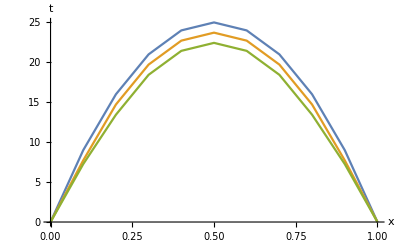

```mathematica
ListLinePlot[Table[Table[{x,u[x,t]},{x,0.,1.,dx}],{t,0.,0.02,dt}],AxesLabel->{"x","t"}]
```

```mathematica
Clear[u]
u[0.,t_]:=u[0.,t]=10
u[1.,t_]:=u[1.,t]=0
u[x_,0.]:=u[x,0.]=100x(1-x)
u[x_,t_?Positive]:=u[x,t]=u[x,t-dt](1-(2 a^2 dt)/dx^2)+(a^2 dt)/dx^2(u[x+dx,t-dt]+u[x-dx,t-dt])
```

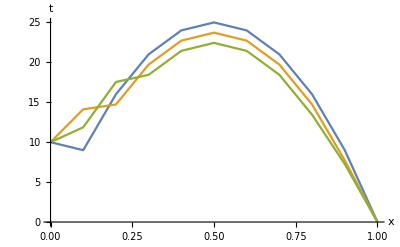

```mathematica
ListLinePlot[Table[Table[{x,u[x,t]},{x,0.,1.,dx}],{t,0.,0.02,dt}],AxesLabel->{"x","t"}]
```

```mathematica
Clear[u]
u[0.,t_]:=u[0.,t]=0
u[1.,t_]:=u[1.,t]=5
u[x_,0.]:=u[x,0.]=100x(1-x)
u[x_,t_?Positive]:=u[x,t]=u[x,t-dt](1-(2 a^2 dt)/dx^2)+(a^2 dt)/dx^2(u[x+dx,t-dt]+u[x-dx,t-dt])
```

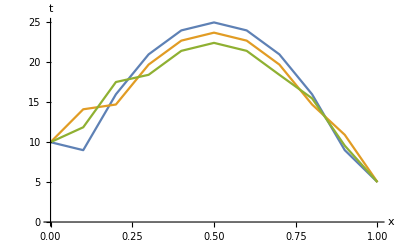

```mathematica
ListLinePlot[Table[Table[{x,u[x,t]},{x,0.,1.,dx}],{t,0.,0.02,dt}],AxesLabel->{"x","t"}]
```

```mathematica
Clear[u]
u[0.,t_]:=u[0.,t]=10
u[1.,t_]:=u[1.,t]=5
u[x_,0.]:=u[x,0.]=100x(1-x)
u[x_,t_?Positive]:=u[x,t]=u[x,t-dt](1-(2 a^2 dt)/dx^2)+(a^2 dt)/dx^2(u[x+dx,t-dt]+u[x-dx,t-dt])
```

```mathematica
ListLinePlot[Table[Table[{x,u[x,t]},{x,0.,1.,dx}],{t,0.,0.02,dt}],AxesLabel->{"x","t"}]
```

-Graphics-